# Kotashevich_S_N Lab_work_2: Символьные вычисления в системе MATHEMATICA

## Задание 1

### 1. Придумайте и определите символьное выражение t1, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением. Последовательно примените к нему функции Expand, ExpandAll, Factor, Together, Apart, Cancel, Simplify и объясните их действие. Выражение t1 должно быть таким, чтобы можно было проследить работу каждой из этих функций.

```mathematica
t1 = (x^2 - 1)/((2 x^2 - 8)(x - y)) + (x + y)^2 + x^2;
```

```mathematica
Expand[t1] (* раскрывает скобки и степени в выражении *)
```

2 x^2-1/((-8+2 x^2) (x-y))+x^2/((-8+2 x^2) (x-y))+2 x y+y^2

```mathematica
ExpandAll[t1] (* раскрывает все скобки и все степени в любой части выражении *)
```

2 x^2+2 x y+y^2-1/(-8 x+2 x^3+8 y-2 x^2 y)+x^2/(-8 x+2 x^3+8 y-2 x^2 y)

```mathematica
Factor[t1] (* раскладывает на целые числа ?????? *)
```

(-1+x^2-16 x^3+4 x^5+8 x y^2-2 x^3 y^2+8 y^3-2 x^2 y^3)/(2 (-2+x) (2+x) (x-y))

```mathematica
Together[t1] (* приводит к общему знаменателю и отменяет расложение *)
```

(-1+x^2-16 x^3+4 x^5+8 x y^2-2 x^3 y^2+8 y^3-2 x^2 y^3)/(2 (-4+x^2) (x-y))

```mathematica
Apart[t1] (* разложить на простые дроби *)
```

2 x^2+2 x y+y^2-((-1+x) (1+x))/(2 (-2+x) (2+x) (-x+y))

```mathematica
Cancel[t1] (* убирает общие множители в числителе и знаменателе *)
```

x^2+(-1+x^2)/(2 (-4+x^2) (x-y))+(x+y)^2

```mathematica
Simplify[t1] (* выполняет последовательность алгебраических и других преобразований над t1 и возвращает простейшую форму *)
```

x^2+(-1+x^2)/((-8+2 x^2) (x-y))+(x+y)^2

### 2. Приведите выражение t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте выражение t2 в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных, например, x в выражении t2 и коэффициент при x^n. Используйте функции Exponent и Coefficient

```mathematica
t2 = Numerator[Together[t1]] (* привести к общему знаменателю, выделить числитель *)
```

-1+x^2-16 x^3+4 x^5+8 x y^2-2 x^3 y^2+8 y^3-2 x^2 y^3

```mathematica
Collect[t2,x] (* собирает вместе объекты, включая одинаковые степени объектов х *)
```

-1+4 x^5+8 x y^2+8 y^3+x^3 (-16-2 y^2)+x^2 (1-2 y^3)

```mathematica
Exponent[t2, x] (* получить максимальную степень x в t2 *)
```

5

```mathematica
Coefficient[t2, x, 5] (* получить коэффициент при х^5 в t2 *)
```

4

## Задание 2

### 1. С помощью функции D вычислите производную функции x^n cos x

```mathematica
D[x^n Cos[x], x] (* получить производную по x *)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

### 2. Вычислите следующие производные

```mathematica
D[a x^3 + 2 x^2, x] (* получить  производную по x *)
```

4 x+3 a x^2

```mathematica
D[4 x^2 - 5 x + 8 - 3/x, {x, 3}] (* получить  производную по x 3 порядка *)
```

18/x^4

```mathematica
D[x^3 y^2 + 3 x^2, {x, 3}, {y, 2}] (* получить смешанная производную по x 3 порядка и по y 2 порядка *)
```

12

### 3. Используя функцию Integrate вычислите интеграл

```mathematica
Integrate[1/(x^2 - 1), x] (* вычислить интеграл *)
```

1/2 Log[1-x]-1/2 Log[1+x]

### 4. Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают с подынтегральными выражениями (при необходимости используйте функции для преобразования выражений)

```mathematica
∫(x^3/(x^2 + 1))ⅆx
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Simplify[D[x^2/2-1/2 Log[1+x^2], x]]
```

x^3/(1+x^2)

```mathematica
∫(1/(x^3 + 1))ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Simplify[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2], x]]
```

1/(1+x^3)

### 5. Вычислите определённый интеграл

```mathematica
∫_1^4 (5 x - 2 √x + 32/x^3)ⅆx
```

259/6

### 6. Вычислите интегралы

```mathematica
∫_0^1 (1 + x^4)^(1/3)ⅆx
```

```mathematica
Hypergeometric2F1[-1/3,1/4,5/4,-1] //N
```

1.05753

```mathematica
∫_0^1. (1 + x^4)^(1/3)ⅆx
```

1.05753

## Задание 3

```mathematica
ClearAll["Global`*"]
```

### 1. Используя функцию Solve, решить уравнение: a x^4 + x^2 + 3 = 0

```mathematica
Solve[a x^4 + x^2 + 3 == 0, x] (* попытка решить уравнение *)
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

### 2. Найти точное решение системы уравнений

```mathematica
Solve[x^2 + y == 1 && y^2 - x^2 == 2, {x, y}, Reals] (* решить одновременные уравнения относительно x и y *)
```

{{x→-√(1/2 (3+√13)),y→1+1/2 (-3-√13)},{x→√(1/2 (3+√13)),y→1+1/2 (-3-√13)}}

### 3. Решить систему уравнений (Если точное решение системы найти не удаётся, получите численное решение)

```mathematica
NSolve[x^2 - y^2 == 1 && y^3 + x == 5, {x, y}] (* получить численное решение уравнений относительно х и у *)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

### 4. Найдите общие решения дифференциальных уравнений, используя функцию DSolve. Самостоятельно задайте граничные условия и найдите соответствующие им частные решения. Постройте их графики

```mathematica
DSolve[y'[x] - y[x] Tan[x] == x, y[x], x] (* решить дифференциальное уравнение для функции y[x] с переменной х *)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
DSolve[y'[x] + y[x] Tan[x] == 1 / Cos[x], y[x], x] (* решить дифференциальное уравнение для функции y[x] с переменной х *)
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

```mathematica
t3 = DSolveValue[{y'[x] - y[x] Tan[x] == x, y[0] == 1}, y[x], x] (* получить решение дифференциальное уравнение для функции y[x] с переменной х с граничными условиями *)
```

1+x Tan[x]

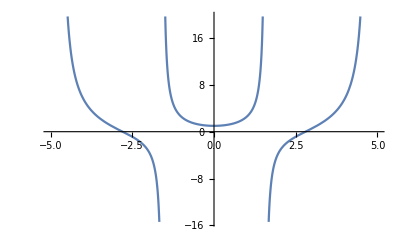

```mathematica
Plot[t3, {x, -5, 5}] (* построить график решения t3 для х от -5 до 5 *)
```

```mathematica
t4 = DSolveValue[{y'[x] + y[x] Tan[x] == 1 / Cos[x], y[0] == 1}, y[x], x] (* получить решение дифференциальное уравнение для функции y[x] с переменной х с граничными условиями *)
```

Cos[x]+Sin[x]

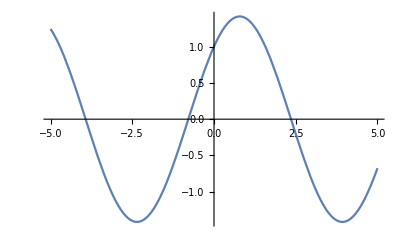

```mathematica
Plot[t4, {x, -5, 5}] (* построить график решения t4 для х от -5 до 5 *)
```

### 5. Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном виде. Затем с помощью функции NDSolve найдите численное решение этого уравнения. Интервал изменения x выберите самостоятельно. На одной координатной плоскости постройте графики численного и символьного решений и покажите, что они совпадают

```mathematica
{{t6 = FullSimplify[DSolveValue[{y''[x] - y'[x] + x y[x] == 0, y[0] == 1, y'[0] == 1}, y[x], x]] (* получить решение дифференциальное уравнение для функции y[x] с переменной х с граничными условиями и упростить его *)}, {□}}
```

{{1/2 ⅇ^(x/2) π (-(AiryAi[1/4]+2 AiryAiPrime[1/4]) AiryBi[1/4-x]+AiryAi[1/4-x] (AiryBi[1/4]+2 AiryBiPrime[1/4]))},{□}}

```mathematica
{{t5 = NDSolveValue[{y''[x] - y'[x] + x y[x] == 0, y[0] == 1, y'[0] == 1}, y[x], {x, -70, 70}] (* получить численное решение дифференциальное уравнение для функции y[x] с переменной х с интревалом от -7 до 7 с граничными условиями *)}, {□}}
```

{{InterpolatingFunction[…][x]},{□}}

```mathematica
Show[Plot[t5, {x, -50, 50}], Plot[t6, {x, -50, 50}, PlotStyle->{Dashed, Red}]] (* объединить два {{графика}, {□}}. второй график представить шрихами красного цвета *)
```

-Graphics-